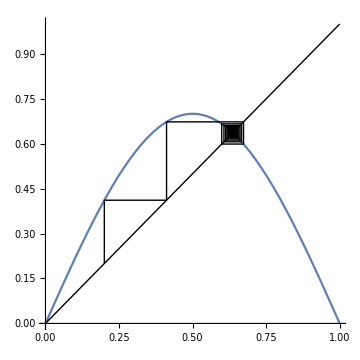

General::munfl: 0.002 5.20259×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.004 5.52081×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.006 3.14419×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

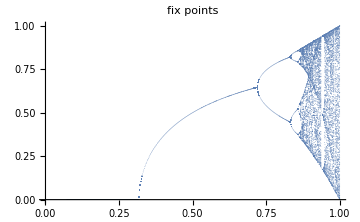

```mathematica
Clear["`*"]
(*start: smallest 0.2, largest: 0.5
a: smallest 0.5 and to 1 
iter: smallest 3
*)
a=0.7; start=0.2;iter=50;

g[x_]:= a Sin[ Pi x];

points=NestList[g,start,iter-1];
lines[x_]:=Line[{{x,x},{x,g[x]},{g[x],g[x]}}];
listlines=lines/@ points;
nstart=500;number=128;
Plot[ g[x],{x,0,1},
AspectRatio->Automatic,
PlotRange->{{0,1},{0,1}},
Epilog->{Line[{{0,0},{1,1}}],listlines},ImageSize->Medium]

afixpoint:=
Union[
Map[
{a,#}&,
NestList[g,Nest[g,start,nstart],number-1]
]
];
amin=0.;amax=1;step=0.002;
fixpoints=Flatten[Table[afixpoint,{a,amin,amax,step}],1];
ListPlot[ fixpoints,
PlotLabel->"fix points",
PlotRange->{{0,1},{0,1}},
PlotStyle->PointSize[0.001]]
```